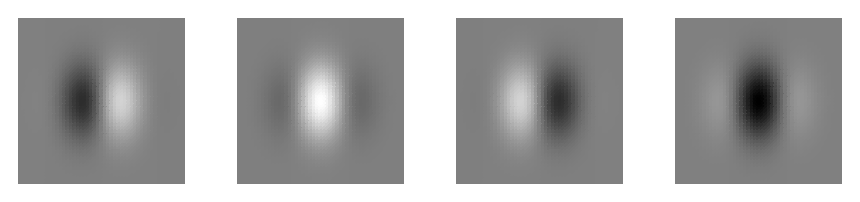

```mathematica
Orientation of Gabor with Phase Nuisance
m=2.3;
k=2.;
GraphicsRow[
Table[
DensityPlot[.5+.5Exp[-x^2-y^2]Cos[k x+ϕ],{x,-m,m},{y,-m,m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->50]
,{ϕ,-π/2,π,π/2}],Background->Gray]
```

θ as Orientation variable, ϕ as phase nuisance

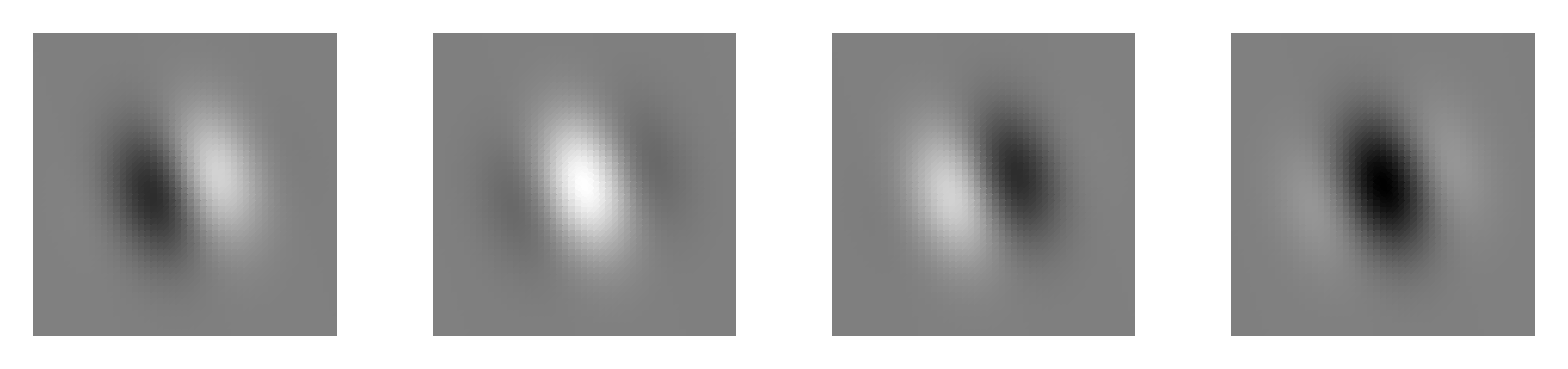

```mathematica
m=2.3;
θ=.3;
k=2.{Cos[θ],Sin[θ]};
GraphicsRow[
Table[
DensityPlot[.5+.5Exp[-x^2-y^2]Cos[k .{x,y}+ϕ],{x,-m,m},{y,-m,m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->50]
,{ϕ,-π/2,π,π/2}],Background->Gray]
```

```mathematica
m=2.3;
θ=.3;
k=2.{Cos[θ],Sin[θ]};
dϕ=2.π/20;
movie=
Table[
DensityPlot[.5+.5Exp[-x^2-y^2]Cos[k .{x,y}+ϕ],{x,-m,m},{y,-m,m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->50]
,{ϕ,dϕ,2π,dϕ}];
Export["/Users/xaq/Presentations/Nonlinear CP/Figures/PhaseMovie1.mov",movie];
```

```mathematica
m=2.3;
ϕ=1.;
k=2.{Cos[θ],Sin[θ]};
dϕ=2.π/40;
movie=
Table[
DensityPlot[.5+.5Exp[-x^2-y^2]Cos[k .{x,y}+ϕ],{x,-m,m},{y,-m,m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->50]
,{θ,dϕ,2π,dϕ}];
Export["/Users/xaq/Presentations/Nonlinear CP/Figures/OrientationMovie1.mov",movie];
```

```mathematica
Clear[k,θ]
Integrate[Exp[-x^2-y^2]Cos[k{Cos[θ],Sin[θ]} .{x,y}+ϕ],{x,-∞,∞},{y,-∞,∞}]
```

ⅇ^(-k^2/4) π Cos[ϕ]

```mathematica
Integrate[Exp[-x^2-y^2+ⅈ (kx x+ky y+ϕ)],{x,-∞,∞},{y,-∞,∞}]
Integrate[Exp[-2 x^2-2 y^2+ⅈ (kx x+ky y+ϕ)],{x,-∞,∞},{y,-∞,∞}]
```

ⅇ^(-kx^2/4-ky^2/4+ⅈ ϕ) π

1/2 ⅇ^(-kx^2/8-ky^2/8+ⅈ ϕ) π

∫ⅆx ⅇ^(-x^2-y^2)Cos[k.x+ϕ]ⅇ^(-x^2-y^2)Cos[k_j.x+ϕ_j] = π/4(ⅇ^(-κ^2/4(1+Cos[θ-θ_j]))Cos[ϕ-ϕ_j]+ⅇ^(-κ^2/4(1-Cos[θ-θ_j]))Cos[ϕ+ϕ_j])

Check it:

```mathematica
Module[{k=6.,θ=0.,ϕ=2.,ϕj=1.,dθ=2.π/60},
data1=Table[NIntegrate[Exp[2(-x^2-y^2)]Cos[k{Cos[θ],Sin[θ]} .{x,y}+ϕ]Cos[k{Cos[θj],Sin[θj]} .{x,y}+ϕj],{x,-∞,∞},{y,-∞,∞}],{θj,0,π/4,dθ}];
data2=Table[π/4(Exp[-k^2/4(1+Cos[θ-θj])]Cos[ϕ+ϕj]+Exp[-k^2/4(1-Cos[θ-θj])]Cos[ϕ-ϕj]),{θj,0,π/4,dθ}]
];
ListPlot[{data1,data2+.01},Joined->True]
```

```mathematica
Manipulate[
Plot[π/4(Exp[-k^2/4(1+Cos[Δθ])]Cos[ϕ+ϕj]+Exp[-k^2/4(1-Cos[Δθ])]Cos[ϕ-ϕj]),{Δθ,0,2π},PlotRange->{-1,1}]
,{{ϕ,0.},0,2π},{{ϕj,0.},0,2π},{{k,2.},.5,5.}]
```

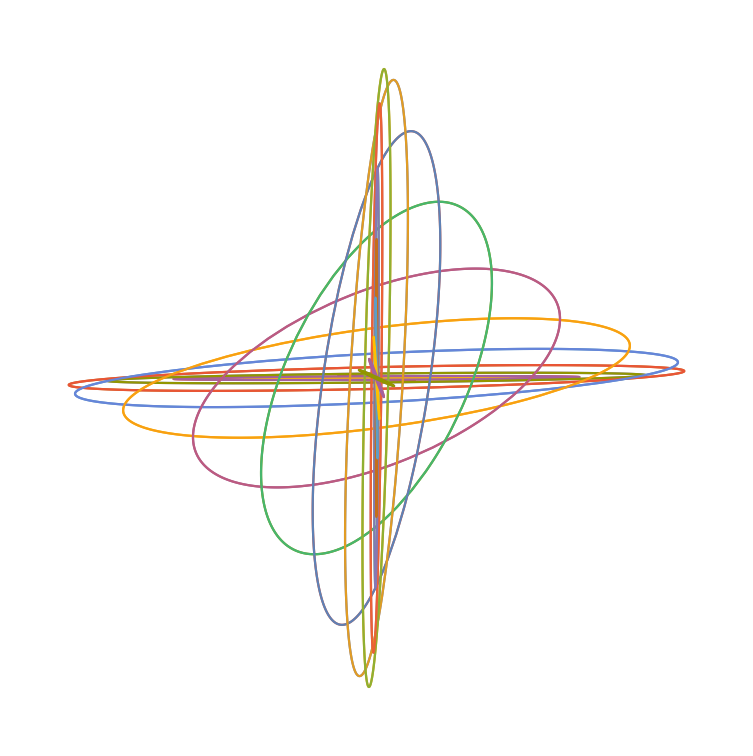

```mathematica
Module[{θ1=1.,θ2=2.,ϕ1=1.,ϕ2=2.,k=5.,δ=2π/40.},
ParametricPlot[Evaluate[Table[{
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]),
π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2])
},{θ,δ,2π,δ}]],{ϕ,0,2π},PlotRange->All,Axes->False]]
```

```mathematica
Module[{θ1=.2,θ2=-.2,ϕ1=1.,ϕ2=2.,k=5.,δ,n=20},
δ=N[π/n];
colorL=Prepend[ConstantArray[Gray,n-1],Directive[Thickness[.015],Red]];
r1=π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]);
r2=π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2]);
θchanging=Table[ParametricPlot[Evaluate[Table[{r1,r2},{θ,δ,π,δ}]],{ϕ,0,2π},PlotRange->All,Axes->False,PlotStyle->RotateRight[colorL,i]]
,{i,n}]];
Export["/Users/xaq/Presentations/Nonlinear CP/Figures/changingAngle.mov",θchanging];
```

```mathematica
ff=FullForm[Plot[{x,2x},{x,0,1}]];
colorL=Extract[ff,Most/@Position[ff,RGBColor,∞]]⟦;;2⟧
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}

```mathematica
Module[{θ1=.2,θ2=-.2,ϕ1=1.,ϕ2=2.,k=5.,δ=2π/40.},
θL={-.4,.4};
circling=Table[
r1=π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]);
r2=π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2]);
ParametricPlot[Evaluate[Table[{r1,r2},{θ,θL}]],{ϕ,0,2π},PlotRange->All,Axes->False,PlotStyle->Thick,Epilog->Table[{colorL⟦i⟧,PointSize->.05,Point[{r1,r2}/.{ϕ->ϕt,θ->θL⟦i⟧}]},{i,2}]],{ϕt,δ,2π,δ}]];
Export["/Users/xaq/Presentations/Nonlinear CP/Figures/Circling.mov",circling];
```

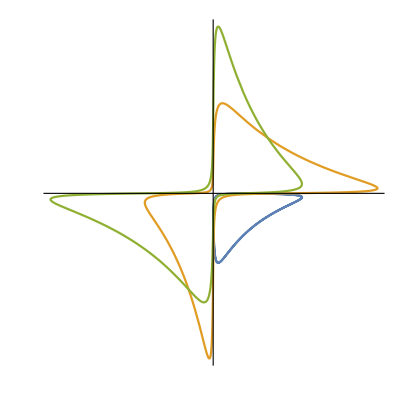

```mathematica
Module[{θ1=1.,θ2=2.,ϕ1=1.,ϕ2=2.,k=5.,δ=2π/40.},
ParametricPlot[Evaluate[Table[{
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]),
π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2])
},{ϕ,{0.,1.,2.}}]],{θ,0,2π},PlotRange->All,Axes->True,Ticks->False]]
```

```mathematica
Module[{θ1=.5,θ2=2.,ϕ1=1.,ϕ2=2.,k=3.,δ=2π/40.},
ParametricPlot3D[{θ,
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]),
π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2])
},{θ,0,2π},{ϕ,0,2π},PlotRange->All,Axes->True,AxesLabel->{"θ","μ_1","μ_2"},Ticks->False]]
```

-Graphics3D-

```mathematica
Module[{θ1=.5,θ2=2.,ϕ1=1.,ϕ2=2.,k=3.,δ=2π/40.},
Show[
ParametricPlot3D[{θ,
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]),
π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2])
},{θ,0,2π},{ϕ,0,2π},PlotRange->All,Axes->True,AxesLabel->{"θ","μ_1","μ_2"},Ticks->False,PlotStyle->Opacity[.5],Mesh->None,Boxed->False],
Table[ParametricPlot3D[{θ,
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1]),
π/4(Exp[-k^2/4(1+Cos[θ-θ2])]Cos[ϕ+ϕ2]+Exp[-k^2/4(1-Cos[θ-θ2])]Cos[ϕ-ϕ2])
},{ϕ,0,2π},PlotRange->All,Axes->True,AxesLabel->{"θ","μ_1","μ_2"},Ticks->False,PlotStyle->Directive[Blue,Thickness[.008]]],{θ,Range[1,1.9,.3]}]]]
```

-Graphics3D-

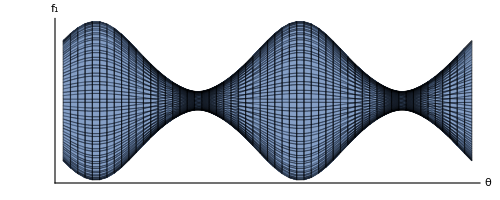

```mathematica
Module[{θ1=.5,θ2=2.,ϕ1=1.,ϕ2=2.,k=3.,δ=2π/40.},
Show[
ParametricPlot[{θ,
π/4(Exp[-k^2/4(1+Cos[θ-θ1])]Cos[ϕ+ϕ1]+Exp[-k^2/4(1-Cos[θ-θ1])]Cos[ϕ-ϕ1])
},{θ,0,2π},{ϕ,0,2π},PlotRange->All,Axes->True,AxesLabel->{"θ","f_1"},Ticks->False,PlotStyle->Opacity[.5],Frame->False,Mesh->All]]]
```

{4.5,9.,13.5}

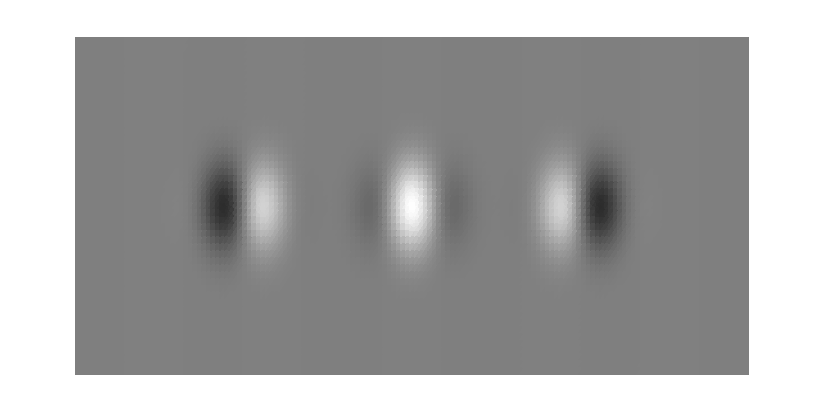

```mathematica
m=4.;
k=2.;
mL=4.5Range[3]
ϕL=π/2 Range[-1,1];
DensityPlot[.5+.5Sum[Exp[-(x-mL⟦i⟧)^2-y^2]Cos[k (x-mL⟦i⟧)+ϕL⟦i⟧],{i,3}],{x,0,4.5m},{y,-m,m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->{150,50},AspectRatio->1/2]
```

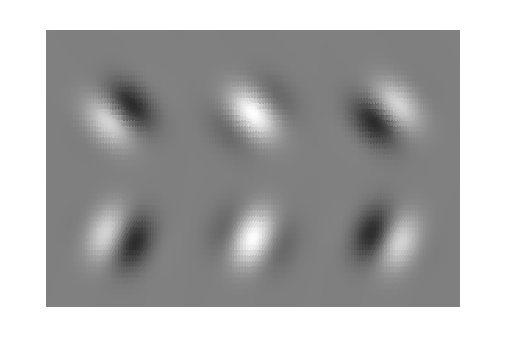

```mathematica
m=4.;
k=2.;
mxL=4.5Range[3];
myL=4.5Range[2];
θL=1.8+{1.,2.};
ϕL=π/2 Range[-1,1];
DensityPlot[.5+.5Sum[Exp[-(x-mxL⟦i⟧)^2-(y-myL⟦j⟧)^2]Cos[k {Cos[θL⟦j⟧],Sin[θL⟦j⟧]}.{x-mxL⟦i⟧,y-myL⟦j⟧}+ϕL⟦i⟧],{i,3},{j,2}],{x,.5m,4m},{y,m/2,3m},PlotRange->{-1,1},ColorFunction->GrayLevel,ColorFunctionScaling->False,Frame->False,PlotPoints->{150,50},AspectRatio->2/3]
```

## Notes

How much more information do we get from R=r r^T than from R=r^2?

## Overlap between two gabors with circular envelopes

```mathematica
g[x_,μ_,σ_,k_,ϕ_]:=Exp[(-(x-μ).(x-μ))/(2 σ^2)]Cos[k.(x-μ)+ϕ]
h[x_,μ_,σ_,k_,ϕ_]:=Exp[(-(x-μ).(x-μ))/(2 σ^2)+ⅈ (k.(x-μ)+ϕ)]
```

```mathematica
Gmn[μ1_,μ2_,σ1_,σ2_,k1_,k2_,ϕ1_,ϕ2_]:=π/(σ1^-2+σ2^-2)Exp[-Norm[μ1]^2/(2 σ1^2)-Norm[μ2]^2/(2 σ2^2)+1/2 Norm[μ1/σ1^2+μ2/σ2^2]^2(σ1^-2+σ2^-2)^-1]*
(Exp[-1/2 Norm[k1+k2]^2/(σ1^-2+σ2^-2)]Cos[(ϕ1-k1.μ1)+(ϕ2-k2.μ2)+((μ1/σ1^2+μ2/σ2^2).(k1+k2))/(σ1^-2+σ2^-2)]
+Exp[-1/2 Norm[k1-k2]^2/(σ1^-2+σ2^-2)]Cos[(ϕ1-k1.μ1)-(ϕ2-k2.μ2)+((μ1/σ1^2+μ2/σ2^2).(k1-k2))/(σ1^-2+σ2^-2)])
```

```mathematica
GmnParts[μ1_,μ2_,σ1_,σ2_,k1_,k2_,ϕ1_,ϕ2_]:=Module[{a=(σ1^-2+σ2^-2),
bp=μ1/σ1^2+μ2/σ2^2+ⅈ (k1+k2),
bm=μ1/σ1^2+μ2/σ2^2+ⅈ (k1-k2),
cp=-Norm[μ1]^2/(2 σ1^2)-Norm[μ2]^2/(2 σ2^2)+ⅈ (ϕ1-k1.μ1+ϕ2-k2.μ2),
cm=-Norm[μ1]^2/(2 σ1^2)-Norm[μ2]^2/(2 σ2^2)+ⅈ (ϕ1-k1.μ1-ϕ2+k2.μ2)},
(*Print[{a,bp,bm,cp,cm}];*)
π/a(Re[Exp[cp+(bp.bp)/(2a)]]+Re[Exp[cm+(bm.bm)/(2a)]])
]
```

```mathematica
(data=Table[{NIntegrate[
g[{x,y},{0,0},1,{0,1},0]*g[{x,y},{0,0},z,{1,0},0]
,{x,-∞,∞},{y,-∞,∞}],
GmnParts[{0,0},{0,0},1,z,{0,1},{1,0},0,0.],
Gmn[{0,0},{0,0},1,z,{0,1},{1,0},0,0.]
},{z,.25,5.,.25}]ᵀ)//MatrixForm
```

(0.348485 | 1.02885 | 1.57811 | 1.90547 | 2.0822 | 2.17678 | 2.2288 | 2.25857 | 2.27633 | 2.28734 | 2.29441 | 2.2991 | 2.3023 | 2.30453 | 2.30613 | 2.3073 | 2.30816 | 2.30881 | 2.30931 | 2.3097
0.348485 | 1.02885 | 1.57811 | 1.90547 | 2.0822 | 2.17678 | 2.2288 | 2.25857 | 2.27633 | 2.28734 | 2.29441 | 2.2991 | 2.30229 | 2.30453 | 2.30613 | 2.3073 | 2.30816 | 2.30881 | 2.30931 | 2.3097
0.348485 | 1.02885 | 1.57811 | 1.90547 | 2.0822 | 2.17678 | 2.2288 | 2.25857 | 2.27633 | 2.28734 | 2.29441 | 2.2991 | 2.30229 | 2.30453 | 2.30613 | 2.3073 | 2.30816 | 2.30881 | 2.30931 | 2.3097)